```mathematica
(* Code for The impact of threshold decision mechansis of collective behaviour *)
(* Morsky, B., Magpantay, F., Day, T., and Akçay, E. *)
Clear["Global`*"]
SetDirectory["/Users/brycemorsky/Documents/Archives/Past research/Penn/Norms and pandemics/figures"];
SetOptions[{Plot,ParametricPlot,ListPlot,ListLinePlot,ListPlot3D},BaseStyle->{FontSize->16},LabelStyle->Directive[FontSize->16],PlotStyle->Thickness[0.008]];
```

```mathematica
(* Parameters *)
γ=0.1;
δ=0.2;
ϵ=1;
κ=1000;
```

```mathematica
(* Functions *)
ρ[p_]=1-η*p;
u[i_,p_,q_] = -β*ρ[p]*i-c*p-θ*(p-q)^2;
BR[i_,p_]=1/(1+Exp[κ*(u[i,0,p]-u[i,1,p])])-p;
SEIR={s'[t]==-β*ρ[p[t]]*s[t]*i[t],e'[t]==β*ρ[p[t]]*s[t]*i[t]-δ*e[t],i'[t]==δ*e[t]-γ*i[t],p'[t]== ϵ*BR[i[t],p[t]]};
ics={s[0]==0.99,e[0]==0.01,i[0]==0.0,p[0]==5.148200222411721*10^(-131)};
SEIRS={s'[t]==-β*ρ[p[t]]*s[t]*i[t]+α*(1-s[t]-e[t]-i[t]),e'[t]==β*ρ[p[t]]*s[t]*i[t]-δ*e[t],i'[t]==δ*e[t]-γ*i[t],p'[t]== ϵ*BR[i[t],p[t]]};
```

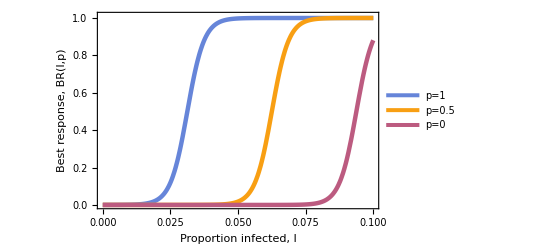

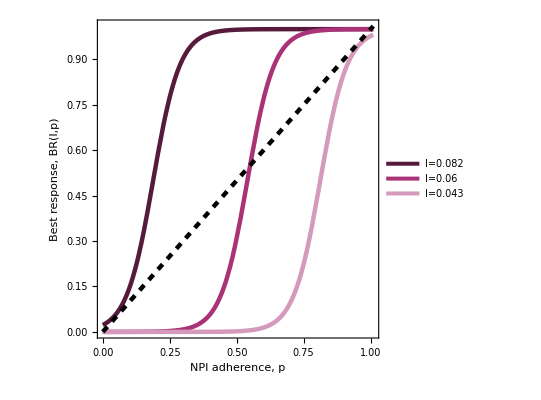

```mathematica
(* Shifts in BR function *)
plt1=Plot[{1/(1+Exp[κ*(u[i,0,p]-u[i,1,p])])/.{p->1,β->0.4,c->0.02,θ->0.01,η->0.8},1/(1+Exp[κ*(u[i,0,p]-u[i,1,p])])/.{p->0.5,β->0.4,c->0.02,θ->0.01,η->0.8},
1/(1+Exp[κ*(u[i,0,p]-u[i,1,p])])/.{p->0,β->0.4,c->0.02,θ->0.01,η->0.8}},{i,0,0.1},PlotRange->{0,1.01},Frame->{True,True,False,False},FrameLabel->{"Proportion infected, I","Best response, BR(I,p)"},PlotLegends->{"p=1","p=0.5","p=0"},PlotPoints->50,PlotStyle->{Directive[ColorData[97][12],Thickness[0.008]],Directive[ColorData[97][13],Thickness[0.008]],Directive[ColorData[97][14],Thickness[0.008]],Directive[Black,Thickness[0.008]]}]
Export["shifts_from_I.png",plt1,ImageResolution->400];
plt2=Plot[{1/(1+Exp[κ*(u[i,0,p]-u[i,1,p])])/.{i->0.082,β->0.4,c->0.02,θ->0.01,η->0.8},1/(1+Exp[κ*(u[i,0,p]-u[i,1,p])])/.{i->0.06,β->0.4,c->0.02,θ->0.01,η->0.8},
1/(1+Exp[κ*(u[i,0,p]-u[i,1,p])])/.{i->0.043,β->0.4,c->0.02,θ->0.01,η->0.8},p},{p,0,1.01},PlotRange->{0,1.01},Frame->{True,True,False,False},FrameLabel->{"NPI adherence, p","Best response, BR(I,p)"},PlotLegends->Placed[LineLegend[{"I=0.082","I=0.06","I=0.043"},LegendLayout->{"Column",1}],{0.872,0.1277}],PlotStyle->{Directive[Blend[{RGBColor["#AA3377"],Black},0.5],Thickness[0.008]],Directive[RGBColor["#AA3377"],Thickness[0.008]],Directive[Blend[{RGBColor["#AA3377"],White},0.5],Thickness[0.008]],Directive[Dashed,Black,Thickness[0.008]]},PlotPoints->50,AspectRatio->1,PlotRangeClipping->False]
Export["shifts_from_p.png",plt2,ImageResolution->400];
```

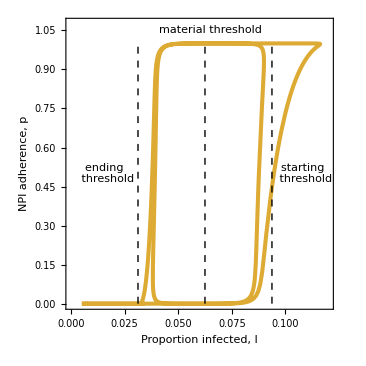

```mathematica
(* Switching *)
sol=NDSolve[Join[SEIR/.{β->0.4,c->0.02,θ->0.01,η->0.8},ics],{s,e,i,p},{t,0,1000}];
plt=Show[ParametricPlot[Evaluate[{i[t],p[t]}/.sol],{t,0,300},PlotRange->{{0.0,0.12},{0.0,1.075}},PlotStyle->{RGBColor["#DDAA33"],Thickness[0.008]},Frame->{True,True,False,False},FrameLabel->{"Proportion infected, I","NPI adherence, p"},AspectRatio->1]/.Line[x_]:>{Arrowheads[Table[0.05,15]],Arrow[x,0.005]},Epilog->{Directive[{Thick,Dashed}],Black,Line[{{0.09375,0},{0.09375,1}}],Line[{{0.0625,0},{0.0625,1}}],Line[{{0.03125,0},{0.03125,1}}],Text[Style["material threshold",Black],{0.065,1.05}],Text[Style["starting \n threshold",Black],{0.10875,0.5}],Text[Style["ending \n threshold",Black],{0.01625,0.5}]},PlotRangeClipping->False,AspectRatio->1]
Export["switch.png",plt,AspectRatio->1,ImageResolution->400];
```

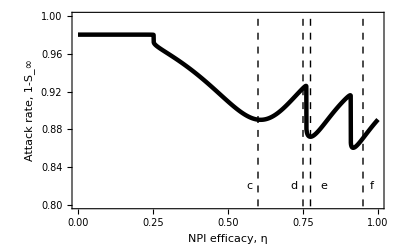

```mathematica
(* eta vs attack rate *)
sfin=Array[n,{2001,2}];
count=1;
Do[
sol=NDSolve[Join[SEIR/.{β->0.4,c->0.02,θ->0.01,η->j/2000},ics],{s,e,i,p},{t,0,1000}];
sfin[[count]]= Join[{0.001*j/2},Evaluate[{1-s[1000]}/.sol][[1]]];
count=count+1;
,{j,0,2000}];
plt=ListLinePlot[sfin,Frame->{True,True,False,False},FrameLabel->{"NPI efficacy, η","Attack rate, 1-S_∞"},PlotRange->{{0,1},{0.8,1}},BaseStyle->{FontSize->16},LabelStyle->Directive[FontSize->16],PlotStyle->{Black,Thickness[0.008]},Epilog->{Directive[{Thick,Dashed,Black}],Line[{{0.6,0},{0.6,1}}],Line[{{0.75,0},{0.75,1}}],Line[{{0.775,0},{0.775,1}}],Line[{{0.95,0},{0.95,1}}],Text["c",{0.57,0.82}],Text["d",{0.72,0.82}],Text["e",{0.82,0.82}],Text["f",{0.98,0.82}]}]
Export["attackrate_eta.png",plt,ImageResolution->400];
```

```mathematica
(* eta time series *)
sol1=NDSolve[Join[SEIR/.{β->0.4,c->0.02,θ->0.01,η->0.6},ics],{s,e,i,p},{t,0,1000}];
plt1=Plot[Evaluate[{s[t],i[t],p[t]}/.sol1],{t,0,300},PlotRange->All,Frame->{True,True,False,False},FrameLabel->{"Time, t","Frequencies"},BaseStyle->{FontSize->16},LabelStyle->Directive[FontSize->16],PlotStyle->{Directive[RGBColor["#004488"],Thickness[0.008]],Directive[RGBColor["#BB5566"],Thickness[0.008]],Directive[RGBColor["#DDAA33"],Thickness[0.008]]},PlotLegends->Placed[{"S","I","p"},{Right,Center}]];
sol2=NDSolve[Join[SEIR/.{β->0.4,c->0.02,θ->0.01,η->0.75},ics],{s,e,i,p},{t,0,1000}];
plt2=Plot[Evaluate[{s[t],i[t],p[t]}/.sol2],{t,0,300},PlotRange->All,Frame->{True,True,False,False},FrameLabel->{"Time, t","Frequencies"},BaseStyle->{FontSize->16},LabelStyle->Directive[FontSize->16],PlotStyle->{Directive[RGBColor["#004488"],Thickness[0.008]],Directive[RGBColor["#BB5566"],Thickness[0.008]],Directive[RGBColor["#DDAA33"],Thickness[0.008]]}];
sol3=NDSolve[Join[SEIR/.{β->0.4,c->0.02,θ->0.01,η->0.775},ics],{s,e,i,p},{t,0,1000}];
plt3=Plot[Evaluate[{s[t],i[t],p[t]}/.sol3],{t,0,300},PlotRange->All,Frame->{True,True,False,False},FrameLabel->{"Time, t","Frequencies"},BaseStyle->{FontSize->16},LabelStyle->Directive[FontSize->16],PlotStyle->{Directive[RGBColor["#004488"],Thickness[0.008]],Directive[RGBColor["#BB5566"],Thickness[0.008]],Directive[RGBColor["#DDAA33"],Thickness[0.008]]}];
sol4=NDSolve[Join[SEIR/.{β->0.4,c->0.02,θ->0.01,η->0.95},ics],{s,e,i,p},{t,0,1000}];
plt4=Plot[Evaluate[{s[t],i[t],p[t]}/.sol4],{t,0,300},PlotRange->All,Frame->{True,True,False,False},FrameLabel->{"Time, t","Frequencies"},BaseStyle->{FontSize->16},LabelStyle->Directive[FontSize->16],PlotStyle->{Directive[RGBColor["#004488"],Thickness[0.008]],Directive[RGBColor["#BB5566"],Thickness[0.008]],Directive[RGBColor["#DDAA33"],Thickness[0.008]]}];
Export["ts_eta_6.png",plt1,ImageResolution->400];
Export["ts_eta_75.png",plt2,ImageResolution->400];
Export["ts_eta_775.png",plt3,ImageResolution->400];
Export["ts_eta_95.png",plt4,ImageResolution->400];
```

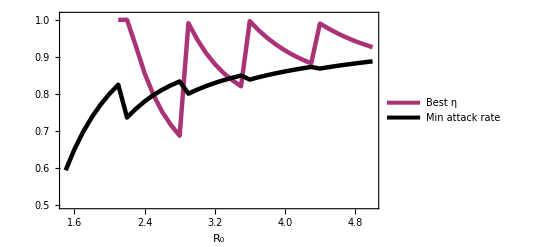

```mathematica
(* Min eta *)
sfin=Array[n,{2001,2}];
sbest=Array[n,{36,2}];
etabest=Array[n,{36,2}];
zeroeta=Array[n,{36,2}];
count1=1;
Do[
count2=1;
Do[
sol=NDSolve[Join[SEIR/.{β->γ*k/10,c->0.02,θ->0.01,η->j/2000},ics],{s,e,i,p},{t,0,1000}];
sfin[[count2]]= Join[{k/10},{0.001*j/2},Evaluate[{1-s[1000]}/.sol][[1]]];
count2=count2+1;
,{j,0,2000}];
etabest[[count1]] = If[k>20,MinimalBy[sfin,Last][[1]][[1;;2]],{Null,Null}];
sbest[[count1]] = MinimalBy[sfin,Last][[1]][[;;;;2]];
zeroeta[[count1]] = sfin[[1]][[;;;;2]];
count1=count1+1;
,{k,15,50}];
plt=ListLinePlot[{etabest,sbest},Frame->{True,True,False,False},FrameLabel->{"R_0"},PlotRange->{{1.5,5},{0.5,1.01}},BaseStyle->{FontSize->16},LabelStyle->Directive[FontSize->16],PlotLegends->Placed[LineLegend[{"Best η","Min attack rate"},LegendLayout->{"Column",1}],{Right,Bottom}],PlotStyle->{Directive[RGBColor["#AA3377"],Thickness[0.008]],Directive[Black,Thickness[0.008]]}]
Export["min_attackrate_eta.png",plt,ImageResolution->400];
```

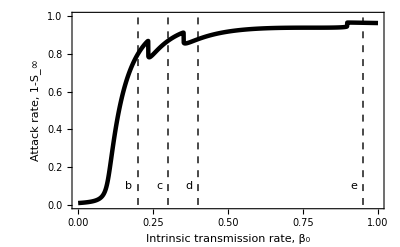

```mathematica
(* beta0 vs attack rate *)
sfin=Array[n,{2000,2}];
count=1;
Do[
sol=NDSolve[Join[SEIR/.{β->j/2000,c->0.02,θ->0.01,η->0.8},ics],{s,e,i,p},{t,0,10000}];
sfin[[count]]= Join[{0.001*j/2},Evaluate[{1-s[10000]}/.sol][[1]]];
count=count+1;
,{j,1,2000}];
plt=ListLinePlot[sfin,Frame->{True,True,False,False},FrameLabel->{"Intrinsic transmission rate, β_0","Attack rate, 1-S_∞"},PlotRange->{{0,1},{0,1}},BaseStyle->{FontSize->16},LabelStyle->Directive[FontSize->16],PlotStyle->{Black,Thickness[0.008]},Epilog->{Directive[{Thick,Dashed}],Line[{{0.2,0},{0.2,1}}],Line[{{0.3,0},{0.3,1}}],Line[{{0.4,0},{0.4,1}}],Line[{{0.95,0},{0.95,1}}],Text["b",{0.17,0.1}],Text["c",{0.27,0.1}],Text["d",{0.37,0.1}],Text["e",{0.92,0.1}]}]
Export["attackrate_beta0.png",plt,ImageResolution->400];
```

```mathematica
(* beta time series *)
sol1=NDSolve[Join[SEIR/.{β->0.2,c->0.02,θ->0.01,η->0.8},ics],{s,e,i,p},{t,0,1000}];
plt1=Plot[Evaluate[{s[t],i[t],p[t]}/.sol1],{t,0,300},PlotRange->All,Frame->{True,True,False,False},FrameLabel->{"Time, t","Frequencies"},BaseStyle->{FontSize->16},PlotStyle->{Directive[RGBColor["#004488"],Thickness[0.008]],Directive[RGBColor["#BB5566"],Thickness[0.008]],Directive[RGBColor["#DDAA33"],Thickness[0.008]]},PlotLegends->Placed[{"S","I","p"},{Right,Center}]];
sol2=NDSolve[Join[SEIR/.{β->0.3,c->0.02,θ->0.01,η->0.8},ics],{s,e,i,p},{t,0,1000}];
plt2=Plot[Evaluate[{s[t],i[t],p[t]}/.sol2],{t,0,300},PlotRange->All,Frame->{True,True,False,False},FrameLabel->{"Time, t","Frequencies"},BaseStyle->{FontSize->16},LabelStyle->Directive[FontSize->16],PlotStyle->{Directive[RGBColor["#004488"],Thickness[0.008]],Directive[RGBColor["#BB5566"],Thickness[0.008]],Directive[RGBColor["#DDAA33"],Thickness[0.008]]}];
sol3=NDSolve[Join[SEIR/.{β->0.5,c->0.02,θ->0.01,η->0.8},ics],{s,e,i,p},{t,0,1000}];
plt3=Plot[Evaluate[{s[t],i[t],p[t]}/.sol3],{t,0,300},PlotRange->All,Frame->{True,True,False,False},FrameLabel->{"Time, t","Frequencies"},BaseStyle->{FontSize->16},LabelStyle->Directive[FontSize->16],PlotStyle->{Directive[RGBColor["#004488"],Thickness[0.008]],Directive[RGBColor["#BB5566"],Thickness[0.008]],Directive[RGBColor["#DDAA33"],Thickness[0.008]]}];
sol4=NDSolve[Join[SEIR/.{β->0.95,c->0.02,θ->0.01,η->0.8},ics],{s,e,i,p},{t,0,1000}];
plt4=Plot[Evaluate[{s[t],i[t],p[t]}/.sol4],{t,0,300},PlotRange->All,Frame->{True,True,False,False},FrameLabel->{"Time, t","Frequencies"},BaseStyle->{FontSize->16},LabelStyle->Directive[FontSize->16],PlotStyle->{Directive[RGBColor["#004488"],Thickness[0.008]],Directive[RGBColor["#BB5566"],Thickness[0.008]],Directive[RGBColor["#DDAA33"],Thickness[0.008]]}];
Export["ts_beta0_2.png",plt1,ImageResolution->400];
Export["ts_beta0_3.png",plt2,ImageResolution->400];
Export["ts_beta0_4.png",plt3,ImageResolution->400];
Export["ts_beta0_95.png",plt4,ImageResolution->400];
```

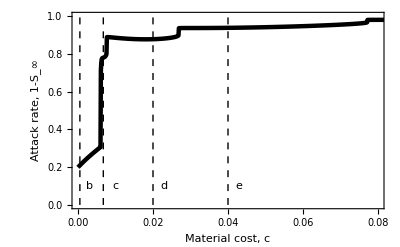

```mathematica
(* c vs attack rate *)
sfin=Array[n,{2001,2}];
count=1;
Do[
sol=NDSolve[Join[SEIR/.{β->0.4,c->j/10000,θ->0.01,η->0.8},ics],{s,e,i,p},{t,0,1000}];
sfin[[count]]= Join[{j/10000},Evaluate[{1-s[1000]}/.sol][[1]]];
count=count+1;
,{j,0,1000}];
plt=ListLinePlot[sfin,Frame->{True,True,False,False},FrameLabel->{"Material cost, c","Attack rate, 1-S_∞"},PlotRange->{{0,0.08},{0,1}},BaseStyle->{FontSize->16},LabelStyle->Directive[FontSize->16],PlotStyle->{Black,Thickness[0.008]},Epilog->{Directive[{Thick,Dashed}],Line[{{0.0005,0},{0.0005,1}}],Line[{{0.00675,0},{0.00675,1}}],Line[{{0.02,0},{0.02,1}}],Line[{{0.04,0},{0.04,1}}],Text["b",{0.003,0.1}],Text["c",{0.01,0.1}],Text["d",{0.023,0.1}],Text["e",{0.043,0.1}]}]
Export["attackrate_c.png",plt,ImageResolution->400];
```

```mathematica
(* c time series *)
sol1=NDSolve[Join[SEIR/.{β->0.4,c->0.0005,θ->0.01,η->0.8},ics],{s,e,i,p},{t,0,1000}];
plt1=Plot[Evaluate[{s[t],i[t],p[t]}/.sol1],{t,0,300},PlotRange->All,Frame->{True,True,False,False},FrameLabel->{"Time, t","Frequencies"},BaseStyle->{FontSize->16},LabelStyle->Directive[FontSize->16],PlotStyle->{Directive[RGBColor["#004488"],Thickness[0.008]],Directive[RGBColor["#BB5566"],Thickness[0.008]],Directive[RGBColor["#DDAA33"],Thickness[0.008]]},PlotLegends->Placed[{"S","I","p"},{Right,Center}]];
sol2=NDSolve[Join[SEIR/.{β->0.4,c->0.00675,θ->0.01,η->0.8},ics],{s,e,i,p},{t,0,1000}];
plt2=Plot[Evaluate[{s[t],i[t],p[t]}/.sol2],{t,0,500},PlotRange->All,Frame->{True,True,False,False},FrameLabel->{"Time, t","Frequencies"},BaseStyle->{FontSize->16},LabelStyle->Directive[FontSize->16],PlotStyle->{Directive[RGBColor["#004488"],Thickness[0.008]],Directive[RGBColor["#BB5566"],Thickness[0.008]],Directive[RGBColor["#DDAA33"],Thickness[0.008]]}];
sol3=NDSolve[Join[SEIR/.{β->0.4,c->0.02,θ->0.01,η->0.8},ics],{s,e,i,p},{t,0,1000}];
plt3=Plot[Evaluate[{s[t],i[t],p[t]}/.sol3],{t,0,300},PlotRange->All,Frame->{True,True,False,False},FrameLabel->{"Time, t","Frequencies"},BaseStyle->{FontSize->16},LabelStyle->Directive[FontSize->16],PlotStyle->{Directive[RGBColor["#004488"],Thickness[0.008]],Directive[RGBColor["#BB5566"],Thickness[0.008]],Directive[RGBColor["#DDAA33"],Thickness[0.008]]}];
sol4=NDSolve[Join[SEIR/.{β->0.4,c->0.04,θ->0.01,η->0.8},ics],{s,e,i,p},{t,0,1000}];
plt4=Plot[Evaluate[{s[t],i[t],p[t]}/.sol4],{t,0,300},PlotRange->All,Frame->{True,True,False,False},FrameLabel->{"Time, t","Frequencies"},BaseStyle->{FontSize->16},LabelStyle->Directive[FontSize->16],PlotStyle->{Directive[RGBColor["#004488"],Thickness[0.008]],Directive[RGBColor["#BB5566"],Thickness[0.008]],Directive[RGBColor["#DDAA33"],Thickness[0.008]]}];
Export["ts_c_0005.png",plt1,ImageResolution->400];
Export["ts_c_00675.png",plt2,ImageResolution->400];
Export["ts_c_02.png",plt3,ImageResolution->400];
Export["ts_c_04.png",plt4,ImageResolution->400];
```

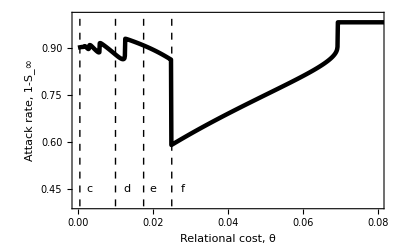

```mathematica
(* theta vs attack rate *)
sfin=Array[n,{1501,2}];
count=1;
Do[
sol=NDSolve[Join[SEIR/.{β->0.4,c->0.02,θ->j/10000,η->0.8},ics],{s,e,i,p},{t,0,1000}];
sfin[[count]]= Join[{j/10000},Evaluate[{1-s[1000]}/.sol][[1]]];
count=count+1;
,{j,0,1500}];
plt=ListLinePlot[sfin,Frame->{True,True,False,False},FrameLabel->{"Relational cost, θ","Attack rate, 1-S_∞"},PlotRange->{{0,0.08},{0.4,1}},BaseStyle->{FontSize->16},LabelStyle->Directive[FontSize->16],PlotStyle->{Black,Thickness[0.008]},Epilog->{Directive[{Thick,Dashed}],Line[{{0.0005,0},{0.0005,1}}],Line[{{0.01,0},{0.01,1}}],Line[{{0.0175,0},{0.0175,1}}],Line[{{0.025,0},{0.025,1}}],Text["c",{0.003,0.45}],Text["d",{0.013,0.45}],Text["e",{0.02,0.45}],Text["f",{0.028,0.45}]}]
Export["attackrate_theta.png",plt,ImageResolution->400];
```

```mathematica
(* theta time series *)
sol1=NDSolve[Join[SEIR/.{β->0.4,c->0.02,θ->0.0005,η->0.8},ics],{s,e,i,p},{t,0,1000}];
plt1=Plot[Evaluate[{s[t],i[t],p[t]}/.sol1],{t,0,300},PlotRange->All,Frame->{True,True,False,False},FrameLabel->{"Time, t","Frequencies"},BaseStyle->{FontSize->16},LabelStyle->Directive[FontSize->16],PlotStyle->{Directive[RGBColor["#004488"],Thickness[0.008]],Directive[RGBColor["#BB5566"],Thickness[0.008]],Directive[RGBColor["#DDAA33"],Thickness[0.008]]},PlotLegends->Placed[{"S","I","p"},{Right,Center}]];
sol2=NDSolve[Join[SEIR/.{β->0.4,c->0.02,θ->0.01,η->0.8},ics],{s,e,i,p},{t,0,1000}];
plt2=Plot[Evaluate[{s[t],i[t],p[t]}/.sol2],{t,0,300},PlotRange->All,Frame->{True,True,False,False},FrameLabel->{"Time, t","Frequencies"},BaseStyle->{FontSize->16},LabelStyle->Directive[FontSize->16],PlotStyle->{Directive[RGBColor["#004488"],Thickness[0.008]],Directive[RGBColor["#BB5566"],Thickness[0.008]],Directive[RGBColor["#DDAA33"],Thickness[0.008]]}];
sol3=NDSolve[Join[SEIR/.{β->0.4,c->0.02,θ->0.0175,η->0.8},ics],{s,e,i,p},{t,0,1000}];
plt3=Plot[Evaluate[{s[t],i[t],p[t]}/.sol3],{t,0,300},PlotRange->All,Frame->{True,True,False,False},FrameLabel->{"Time, t","Frequencies"},BaseStyle->{FontSize->16},LabelStyle->Directive[FontSize->16],PlotStyle->{Directive[RGBColor["#004488"],Thickness[0.008]],Directive[RGBColor["#BB5566"],Thickness[0.008]],Directive[RGBColor["#DDAA33"],Thickness[0.008]]}];
sol4=NDSolve[Join[SEIR/.{β->0.4,c->0.02,θ->0.025,η->0.8},ics],{s,e,i,p},{t,0,1000}];
plt4=Plot[Evaluate[{s[t],i[t],p[t]}/.sol4],{t,0,300},PlotRange->All,Frame->{True,True,False,False},FrameLabel->{"Time, t","Frequencies"},BaseStyle->{FontSize->16},LabelStyle->Directive[FontSize->16],PlotStyle->{Directive[RGBColor["#004488"],Thickness[0.008]],Directive[RGBColor["#BB5566"],Thickness[0.008]],Directive[RGBColor["#DDAA33"],Thickness[0.008]]}];
Export["ts_theta_0005.png",plt1,ImageResolution->400];
Export["ts_theta_01.png",plt2,ImageResolution->400];
Export["ts_theta_0175.png",plt3,ImageResolution->400];
Export["ts_theta_025.png",plt4,ImageResolution->400];
```

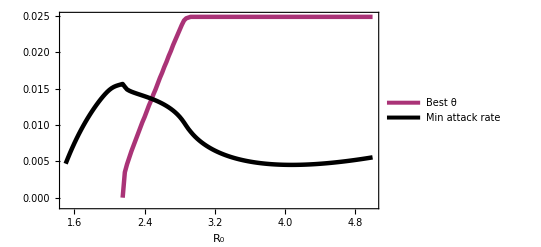

```mathematica
(* Min theta *)
sfin=Array[n,{1501,2}];
sbest=Array[n,{141,2}];
thetabest=Array[n,{141,2}];
count1=1;
Do[
count2=1;
Do[
sol=NDSolve[Join[SEIR/.{β->γ*k/40,c->0.02,θ->j/10000,η->0.8},ics],{s,e,i,p},{t,0,1000}];
sfin[[count2]]= Join[{k/40},{j/10000},Evaluate[{(0.5-s[1000])/20}/.sol][[1]]];
count2=count2+1;
,{j,0,1500}];
thetabest[[count1]] =  If[k≥86,MinimalBy[sfin,Last][[1]][[1;;2]],{Null,Null}];
sbest[[count1]] = MinimalBy[sfin,Last][[1]][[;;;;2]];
count1=count1+1;
,{k,60,200}];
plt=ListLinePlot[{thetabest,sbest},PlotRange->{{1.5,5},{-0.001,0.025}},BaseStyle->{FontSize->16},LabelStyle->Directive[FontSize->16],PlotLegends->Placed[LineLegend[{"Best θ","Min attack rate"},LegendLayout->{"Column",1}],{Right,Center}],PlotStyle->{Directive[RGBColor["#AA3377"],Thickness[0.008]],Directive[Black,Thickness[0.008]]},Frame->{{True,True},{True,False}},FrameTicks-> {{True,{{0.000,0.5},{0.005,0.6},{0.01,0.7},{0.015,0.8},{0.02,0.9},{0.025,1}}},{True,False}},FrameLabel->{"R_0"},FrameStyle-> {Automatic,Directive[FontColor->RGBColor["#AA3377"]],Automatic,Directive[FontColor->Black]}]
Export["min_attackrate_theta.png",plt,ImageResolution->400];
```

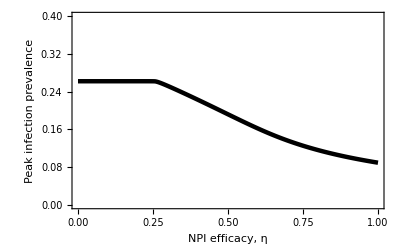

```mathematica
(* eta vs peak infection prevalence *)
peakI=Array[n,{2001,2}];
count=1;
Do[
sol=NDSolve[Join[SEIR/.{β->0.4,c->0.02,θ->0.01,η->j/2000},ics],{s,e,i,p},{t,0,1000}];
solutionI[t_?NumericQ]:=First[i/.sol][t];
peakI[[count]]= {0.001*j/2,NMaximize[{solutionI[t],0<t<100},t,WorkingPrecision->10][[1]]};
count=count+1;
,{j,0,2000}];
plt=ListLinePlot[peakI,Frame->{True,True,False,False},FrameLabel->{"NPI efficacy, η","Peak infection prevalence"},PlotRange->{{0,1},{0,0.4}},BaseStyle->{FontSize->16},LabelStyle->Directive[FontSize->16],PlotStyle->{Black,Thickness[0.008]}]
Export["peak_infection.png",plt,ImageResolution->400];
```

## Two type model

```mathematica
u2T[i_,p_,q_,c_,θ_] = -β*ρ[p]*i-c*p-θ*(p-q)^2;
BR2T[i_,p_,pbar_,c_,θ_]=1/(1+Exp[κ*(u2T[i,0,pbar,c,θ]-u2T[i,1,pbar,c,θ])])-p;
SEIR2T={s1'[t]==-β*ρ[p1[t]]*s1[t]*i[t],s2'[t]==-β*ρ[p2[t]]*s2[t]*i[t],e'[t]==β*(ρ[p1[t]]*s1[t]+ρ[p2[t]]*s2[t])*i[t]-δ*e[t],i'[t]==δ*e[t]-γ*i[t],p1'[t]== ϵ*BR2T[i[t],p1[t],pbar1,c1,θ1],p2'[t]== ϵ*BR2T[i[t],p2[t],pbar2,c2,θ2]};
ics2T={s1[0]==0.495,s2[0]==0.495,e[0]==0.005,i[0]==0.005,p1[0]==5.148200222411721*10^(-131),p2[0]==5.148200222411721*10^(-131)};
```

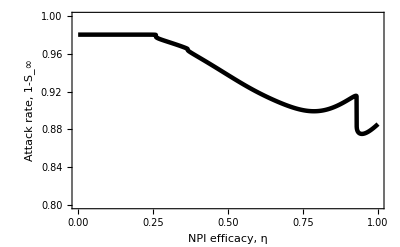

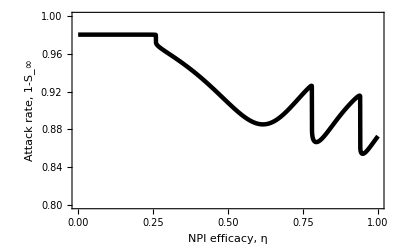

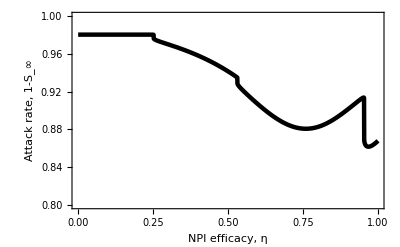

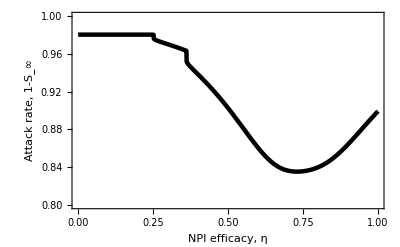

```mathematica
(* eta vs attack rate *)
sfin=Array[n,{2000,2}];
count=1;
Do[
sol=NDSolve[Join[SEIR2T/.{β->0.4,pbar1->(s1[t]*p1[t]+s2[t]*p2[t])/(s1[t]+s2[t]),pbar2->(s1[t]*p1[t]+s2[t]*p2[t])/(s1[t]+s2[t]),c1->0.02,c2->0.04,θ1->0.01,θ2->0.01,η->j/2000},ics2T],{s1,s2,e,i,p1,p2},{t,0,10000}];
sfin[[count]]= Join[{0.001*j/2},Evaluate[{1-s1[10000]-s2[10000]}/.sol][[1]]];
count=count+1;
,{j,1,2000}];
plt1=ListLinePlot[sfin,Frame->{True,True,False,False},FrameLabel->{"NPI efficacy, η","Attack rate, 1-S_∞"},PlotRange->{{0,1},{0.8,1}},BaseStyle->{FontSize->16},LabelStyle->Directive[FontSize->16],PlotStyle->{Black,Thickness[0.008]}]
Export["attackrate_2Tc_eta.png",plt1,ImageResolution->400];
sfin=Array[n,{2000,2}];
count=1;
Do[
sol=NDSolve[Join[SEIR2T/.{β->0.4,pbar1->(s1[t]*p1[t]+s2[t]*p2[t])/(s1[t]+s2[t]),pbar2->(s1[t]*p1[t]+s2[t]*p2[t])/(s1[t]+s2[t]),c1->0.02,c2->0.02,θ1->0.01,θ2->0.02,η->j/2000},ics2T],{s1,s2,e,i,p1,p2},{t,0,10000}];
sfin[[count]]= Join[{0.001*j/2},Evaluate[{1-s1[10000]-s2[10000]}/.sol][[1]]];
count=count+1;
,{j,1,2000}];
plt2=ListLinePlot[sfin,Frame->{True,True,False,False},FrameLabel->{"NPI efficacy, η","Attack rate, 1-S_∞"},PlotRange->{{0,1},{0.8,1}},BaseStyle->{FontSize->16},LabelStyle->Directive[FontSize->16],PlotStyle->{Black,Thickness[0.008]}]
Export["attackrate_2Ttheta_eta.png",plt2,ImageResolution->400];
sfin=Array[n,{2000,2}];
count=1;
Do[
sol=NDSolve[Join[SEIR2T/.{β->0.4,pbar1->p1[t],pbar2->p2[t],c1->0.02,c2->0.04,θ1->0.01,θ2->0.01,η->j/2000},ics2T],{s1,s2,e,i,p1,p2},{t,0,10000}];
sfin[[count]]= Join[{0.001*j/2},Evaluate[{1-s1[10000]-s2[10000]}/.sol][[1]]];
count=count+1;
,{j,1,2000}];
plt3=ListLinePlot[sfin,Frame->{True,True,False,False},FrameLabel->{"NPI efficacy, η","Attack rate, 1-S_∞"},PlotRange->{{0,1},{0.8,1}},BaseStyle->{FontSize->16},LabelStyle->Directive[FontSize->16],PlotStyle->{Black,Thickness[0.008]}]
Export["attackrate_2Thomophilyc_eta.png",plt3,ImageResolution->400];
sfin=Array[n,{2000,2}];
count=1;
Do[
sol=NDSolve[Join[SEIR2T/.{β->0.4,pbar1->p1[t],pbar2->p2[t],c1->0.02,c2->0.02,θ1->0.01,θ2->0.02,η->j/2000},ics2T],{s1,s2,e,i,p1,p2},{t,0,10000}];
sfin[[count]]= Join[{0.001*j/2},Evaluate[{1-s1[10000]-s2[10000]}/.sol][[1]]];
count=count+1;
,{j,1,2000}];
plt4=ListLinePlot[sfin,Frame->{True,True,False,False},FrameLabel->{"NPI efficacy, η","Attack rate, 1-S_∞"},PlotRange->{{0,1},{0.8,1}},BaseStyle->{FontSize->16},LabelStyle->Directive[FontSize->16],PlotStyle->{Black,Thickness[0.008]}]
Export["attackrate_2Thomophilytheta_eta.png",plt4,ImageResolution->400];
```

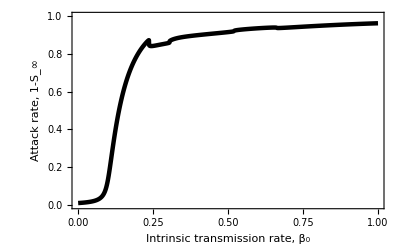

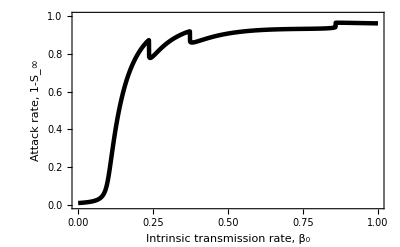

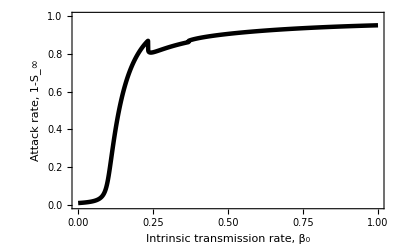

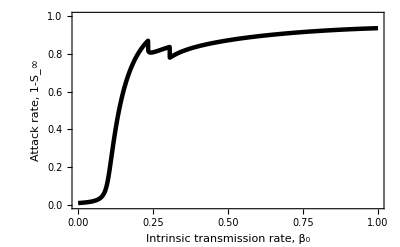

```mathematica
(* beta vs attack rate *)
sfin=Array[n,{2000,2}];
count=1;
Do[
sol=NDSolve[Join[SEIR2T/.{pbar1->(s1[t]*p1[t]+s2[t]*p2[t])/(s1[t]+s2[t]),pbar2->(s1[t]*p1[t]+s2[t]*p2[t])/(s1[t]+s2[t]),β->j/2000,c1->0.02,c2->0.04,θ1->0.01,θ2->0.01,η->0.8},ics2T],{s1,s2,e,i,p1,p2},{t,0,10000}];
sfin[[count]]= Join[{0.001*j/2},Evaluate[{1-s1[10000]-s2[10000]}/.sol][[1]]];
count=count+1;
,{j,1,2000}];
plt1=ListLinePlot[sfin,Frame->{True,True,False,False},FrameLabel->{"Intrinsic transmission rate, β_0","Attack rate, 1-S_∞"},PlotRange->{{0,1},{0,1}},BaseStyle->{FontSize->16},LabelStyle->Directive[FontSize->16],PlotStyle-> {Black,Thickness[0.008]}]
Export["attackrate_2Tc_beta.png",plt1,ImageResolution->400];
sfin=Array[n,{2000,2}];
count=1;
Do[
sol=NDSolve[Join[SEIR2T/.{pbar1->(s1[t]*p1[t]+s2[t]*p2[t])/(s1[t]+s2[t]),pbar2->(s1[t]*p1[t]+s2[t]*p2[t])/(s1[t]+s2[t]),β->j/2000,c1->0.02,c2->0.02,θ1->0.01,θ2->0.02,η->0.8},ics2T],{s1,s2,e,i,p1,p2},{t,0,10000}];
sfin[[count]]= Join[{0.001*j/2},Evaluate[{1-s1[10000]-s2[10000]}/.sol][[1]]];
count=count+1;
,{j,1,2000}];
plt2=ListLinePlot[sfin,Frame->{True,True,False,False},FrameLabel->{"Intrinsic transmission rate, β_0","Attack rate, 1-S_∞"},PlotRange->{{0,1},{0,1}},BaseStyle->{FontSize->16},LabelStyle->Directive[FontSize->16],PlotStyle-> {Black,Thickness[0.008]}]
Export["attackrate_2Ttheta_beta.png",plt2,ImageResolution->400];
sfin=Array[n,{2000,2}];
count=1;
Do[
sol=NDSolve[Join[SEIR2T/.{pbar1->p1[t],pbar2->p2[t],β->j/2000,c1->0.02,c2->0.04,θ1->0.01,θ2->0.01,η->0.8},ics2T],{s1,s2,e,i,p1,p2},{t,0,10000}];
sfin[[count]]= Join[{0.001*j/2},Evaluate[{1-s1[10000]-s2[10000]}/.sol][[1]]];
count=count+1;
,{j,1,2000}];
plt3=ListLinePlot[sfin,Frame->{True,True,False,False},FrameLabel->{"Intrinsic transmission rate, β_0","Attack rate, 1-S_∞"},PlotRange->{{0,1},{0,1}},BaseStyle->{FontSize->16},LabelStyle->Directive[FontSize->16],PlotStyle->{Black,Thickness[0.008]}]
Export["attackrate_2Thomophilyc_beta.png",plt3,ImageResolution->400];
sfin=Array[n,{2000,2}];
count=1;
Do[
sol=NDSolve[Join[SEIR2T/.{pbar1->p1[t],pbar2->p2[t],β->j/2000,c1->0.02,c2->0.02,θ1->0.01,θ2->0.02,η->0.8},ics2T],{s1,s2,e,i,p1,p2},{t,0,10000}];
sfin[[count]]= Join[{0.001*j/2},Evaluate[{1-s1[10000]-s2[10000]}/.sol][[1]]];
count=count+1;
,{j,1,2000}];
plt4=ListLinePlot[sfin,Frame->{True,True,False,False},FrameLabel->{"Intrinsic transmission rate, β_0","Attack rate, 1-S_∞"},PlotRange->{{0,1},{0,1}},BaseStyle->{FontSize->16},LabelStyle->Directive[FontSize->16],PlotStyle->{Black,Thickness[0.008]}]
Export["attackrate_2Thomophilytheta_beta.png",plt4,ImageResolution->400];
```

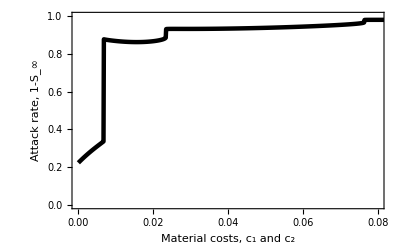

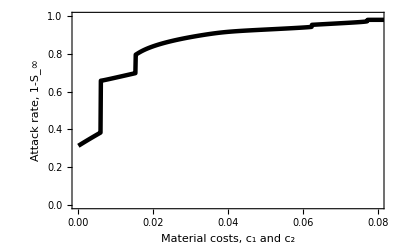

```mathematica
(* c vs attack rate *)
sfin=Array[n,{2000,2}];
count=1;
Do[
sol=NDSolve[Join[SEIR2T/.{β->0.4,pbar1->(s1[t]*p1[t]+s2[t]*p2[t])/(s1[t]+s2[t]),pbar2->(s1[t]*p1[t]+s2[t]*p2[t])/(s1[t]+s2[t]),c1->j/10000,c2->j/10000,θ1->0.01,θ2->0.02,η->0.8},ics2T],{s1,s2,e,i,p1,p2},{t,0,10000}];
sfin[[count]]= Join[{j/10000},Evaluate[{1-s1[10000]-s2[10000]}/.sol][[1]]];
count=count+1;
,{j,1,1000}];
plt2=ListLinePlot[sfin,Frame->{True,True,False,False},FrameLabel->{"Material costs, c_1 and c_2","Attack rate, 1-S_∞"},PlotRange->{{0,0.08},{0,1}},BaseStyle->{FontSize->16},LabelStyle->Directive[FontSize->16],PlotStyle-> {Black,Thickness[0.008]}]
Export["attackrate_2Ttheta_c.png",plt2,ImageResolution->400];
sfin=Array[n,{2000,2}];
count=1;
Do[
sol=NDSolve[Join[SEIR2T/.{β->0.4,pbar1->p1[t],pbar2->p2[t],c1->j/10000,c2->j/10000,θ1->0.01,θ2->0.02,η->0.8},ics2T],{s1,s2,e,i,p1,p2},{t,0,10000}];
sfin[[count]]= Join[{j/10000},Evaluate[{1-s1[10000]-s2[10000]}/.sol][[1]]];
count=count+1;
,{j,1,1000}];
plt4=ListLinePlot[sfin,Frame->{True,True,False,False},FrameLabel->{"Material costs, c_1 and c_2","Attack rate, 1-S_∞"},PlotRange->{{0,0.08},{0,1}},BaseStyle->{FontSize->16},LabelStyle->Directive[FontSize->16],PlotStyle-> {Black,Thickness[0.008]}]
Export["attackrate_2Thomophilytheta_c.png",plt4,ImageResolution->400];
```

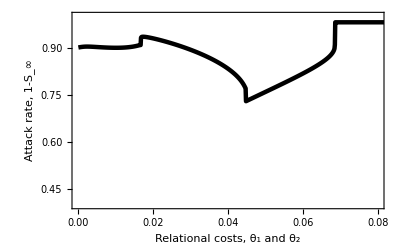

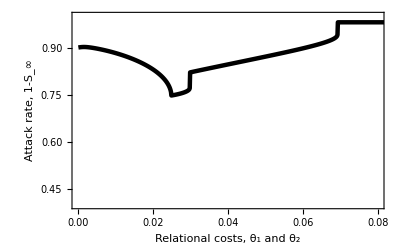

```mathematica
(* theta vs attack rate *)
sfin=Array[n,{2000,2}];
count=1;
Do[
sol=NDSolve[Join[SEIR2T/.{β->0.4,pbar1->(s1[t]*p1[t]+s2[t]*p2[t])/(s1[t]+s2[t]),pbar2->(s1[t]*p1[t]+s2[t]*p2[t])/(s1[t]+s2[t]),c1->0.02,c2->0.04,θ1->j/10000,θ2->j/10000,η->0.8},ics2T],{s1,s2,e,i,p1,p2},{t,0,10000}];
sfin[[count]]= Join[{j/10000},Evaluate[{1-s1[10000]-s2[10000]}/.sol][[1]]];
count=count+1;
,{j,1,1000}];
plt2=ListLinePlot[sfin,Frame->{True,True,False,False},FrameLabel->{"Relational costs, θ_1 and θ_2","Attack rate, 1-S_∞"},PlotRange->{{0,0.08},{0.4,1}},BaseStyle->{FontSize->16},LabelStyle->Directive[FontSize->16],PlotStyle-> {Black,Thickness[0.008]}]
Export["attackrate_2Tc_theta.png",plt2,ImageResolution->400];
sfin=Array[n,{2000,2}];
count=1;
Do[
sol=NDSolve[Join[SEIR2T/.{β->0.4,pbar1->p1[t],pbar2->p2[t],c1->0.02,c2->0.04,θ1->j/10000,θ2->j/10000,η->0.8},ics2T],{s1,s2,e,i,p1,p2},{t,0,10000}];
sfin[[count]]= Join[{j/10000},Evaluate[{1-s1[10000]-s2[10000]}/.sol][[1]]];
count=count+1;
,{j,1,1000}];
plt4=ListLinePlot[sfin,Frame->{True,True,False,False},FrameLabel->{"Relational costs, θ_1 and θ_2","Attack rate, 1-S_∞"},PlotRange->{{0,0.08},{0.4,1}},BaseStyle->{FontSize->16},LabelStyle->Directive[FontSize->16],PlotStyle->{Black,Thickness[0.008]}]
Export["attackrate_2Thomophilyc_theta.png",plt4,ImageResolution->400];
```

```mathematica
Biased beliefs
```

```mathematica
BRbias[i_,p_]=1/(1+Exp[κ*(u[i,0,p*(1-ϕ)+χ*ϕ]-u[i,1,p*(1-ϕ)+χ*ϕ])])-p;
SEIRbias={s'[t]==-β*ρ[p[t]]*s[t]*i[t],e'[t]==β*ρ[p[t]]*s[t]*i[t]-δ*e[t],i'[t]==δ*e[t]-γ*i[t],p'[t]== ϵ*BRbias[i[t],p[t]]};
```

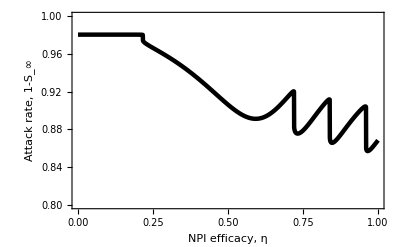

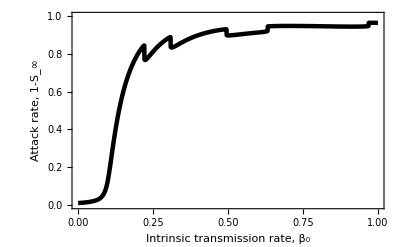

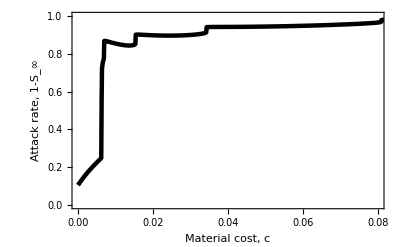

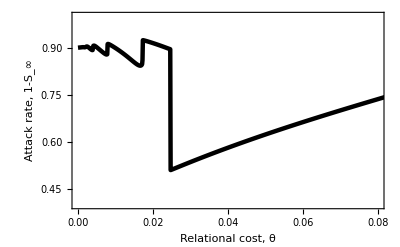

```mathematica
(* optimism/positive bias *)
sfin=Array[n,{2001,2}];
count=1;
Do[
sol=NDSolve[Join[SEIRbias/.{ϕ->0.2,χ->1,β->0.4,c->0.02,θ->0.01,η->j/2000},ics],{s,e,i,p},{t,0,1000}];
sfin[[count]]= Join[{0.001*j/2},Evaluate[{1-s[1000]}/.sol][[1]]];
count=count+1;
,{j,0,2000}];
plt1=ListLinePlot[sfin,Frame->{True,True,False,False},FrameLabel->{"NPI efficacy, η","Attack rate, 1-S_∞"},PlotRange->{{0,1},{0.8,1}},BaseStyle->{FontSize->16},LabelStyle->Directive[FontSize->16],PlotStyle->{Black,Thickness[0.008]}]
Export["attackrate_posbias_eta.png",plt1,ImageResolution->400];
sfin=Array[n,{2000,2}];
count=1;
Do[
sol=NDSolve[Join[SEIRbias/.{ϕ->0.2,χ->1,β->j/2000,c->0.02,θ->0.01,η->0.8},ics],{s,e,i,p},{t,0,10000}];
sfin[[count]]= Join[{0.001*j/2},Evaluate[{1-s[10000]}/.sol][[1]]];
count=count+1;
,{j,1,2000}];
plt2=ListLinePlot[sfin,Frame->{True,True,False,False},FrameLabel->{"Intrinsic transmission rate, β_0","Attack rate, 1-S_∞"},PlotRange->{{0,1},{0,1}},BaseStyle->{FontSize->16},LabelStyle->Directive[FontSize->16],PlotStyle->{Black,Thickness[0.008]}]
Export["attackrate_posbias_beta.png",plt2,ImageResolution->400];
sfin=Array[n,{2001,2}];
count=1;
Do[
sol=NDSolve[Join[SEIRbias/.{ϕ->0.2,χ->1,β->0.4,c->j/10000,θ->0.01,η->0.8},ics],{s,e,i,p},{t,0,1000}];
sfin[[count]]= Join[{j/10000},Evaluate[{1-s[1000]}/.sol][[1]]];
count=count+1;
,{j,0,1000}];
plt3=ListLinePlot[sfin,Frame->{True,True,False,False},FrameLabel->{"Material cost, c","Attack rate, 1-S_∞"},PlotRange->{{0,0.08},{0,1}},BaseStyle->{FontSize->16},LabelStyle->Directive[FontSize->16],PlotStyle->{Black,Thickness[0.008]}]
Export["attackrate_posbias_c.png",plt3,ImageResolution->400];
sfin=Array[n,{1501,2}];
count=1;
Do[
sol=NDSolve[Join[SEIRbias/.{ϕ->0.2,χ->1,β->0.4,c->0.02,θ->j/10000,η->0.8},ics],{s,e,i,p},{t,0,1000}];
sfin[[count]]= Join[{j/10000},Evaluate[{1-s[1000]}/.sol][[1]]];
count=count+1;
,{j,0,1500}];
plt4=ListLinePlot[sfin,Frame->{True,True,False,False},FrameLabel->{"Relational cost, θ","Attack rate, 1-S_∞"},PlotRange->{{0,0.08},{0.4,1}},BaseStyle->{FontSize->16},LabelStyle->Directive[FontSize->16],PlotStyle->{Black,Thickness[0.008]}]
Export["attackrate_posbias_theta.png",plt4,ImageResolution->400];
```

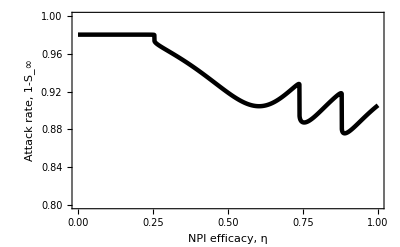

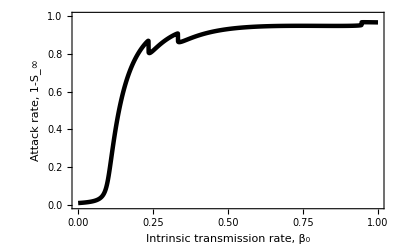

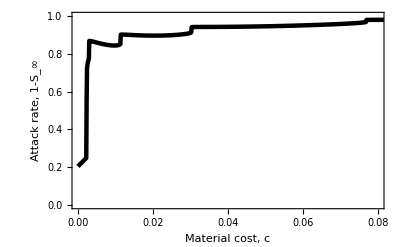

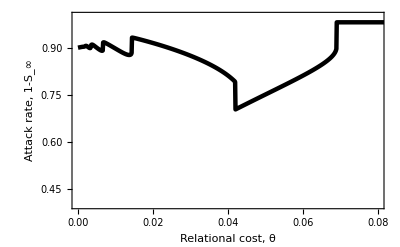

```mathematica
(* pessimism/negative bias *)
sfin=Array[n,{2001,2}];
count=1;
Do[
sol=NDSolve[Join[SEIRbias/.{ϕ->0.2,χ->0,β->0.4,c->0.02,θ->0.01,η->j/2000},ics],{s,e,i,p},{t,0,1000}];
sfin[[count]]= Join[{0.001*j/2},Evaluate[{1-s[1000]}/.sol][[1]]];
count=count+1;
,{j,0,2000}];
plt1=ListLinePlot[sfin,Frame->{True,True,False,False},FrameLabel->{"NPI efficacy, η","Attack rate, 1-S_∞"},PlotRange->{{0,1},{0.8,1}},BaseStyle->{FontSize->16},LabelStyle->Directive[FontSize->16],PlotStyle->{Black,Thickness[0.008]}]
Export["attackrate_negbias_eta.png",plt1,ImageResolution->400];
sfin=Array[n,{2000,2}];
count=1;
Do[
sol=NDSolve[Join[SEIRbias/.{ϕ->0.2,χ->0,β->j/2000,c->0.02,θ->0.01,η->0.8},ics],{s,e,i,p},{t,0,10000}];
sfin[[count]]= Join[{0.001*j/2},Evaluate[{1-s[10000]}/.sol][[1]]];
count=count+1;
,{j,1,2000}];
plt2=ListLinePlot[sfin,Frame->{True,True,False,False},FrameLabel->{"Intrinsic transmission rate, β_0","Attack rate, 1-S_∞"},PlotRange->{{0,1},{0,1}},BaseStyle->{FontSize->16},LabelStyle->Directive[FontSize->16],PlotStyle->{Black,Thickness[0.008]}]
Export["attackrate_negbias_beta.png",plt2,ImageResolution->400];
sfin=Array[n,{2001,2}];
count=1;
Do[
sol=NDSolve[Join[SEIRbias/.{ϕ->0.2,χ->0,β->0.4,c->j/10000,θ->0.01,η->0.8},ics],{s,e,i,p},{t,0,1000}];
sfin[[count]]= Join[{j/10000},Evaluate[{1-s[1000]}/.sol][[1]]];
count=count+1;
,{j,0,1000}];
plt3=ListLinePlot[sfin,Frame->{True,True,False,False},FrameLabel->{"Material cost, c","Attack rate, 1-S_∞"},PlotRange->{{0,0.08},{0,1}},BaseStyle->{FontSize->16},LabelStyle->Directive[FontSize->16],PlotStyle-> {Black,Thickness[0.008]}]
Export["attackrate_negbias_c.png",plt3,ImageResolution->400];
sfin=Array[n,{1501,2}];
count=1;
Do[
sol=NDSolve[Join[SEIRbias/.{ϕ->0.2,χ->0,β->0.4,c->0.02,θ->j/10000,η->0.8},ics],{s,e,i,p},{t,0,1000}];
sfin[[count]]= Join[{j/10000},Evaluate[{1-s[1000]}/.sol][[1]]];
count=count+1;
,{j,0,1500}];
plt4=ListLinePlot[sfin,Frame->{True,True,False,False},FrameLabel->{"Relational cost, θ","Attack rate, 1-S_∞"},PlotRange->{{0,0.08},{0.4,1}},BaseStyle->{FontSize->16},LabelStyle->Directive[FontSize->16],PlotStyle-> {Black,Thickness[0.008]}]
Export["attackrate_negbias_theta.png",plt4,ImageResolution->400];
```